```mathematica
deps={"ApplicationConfiguration"->"Util","Business"->"Dashboard","Business"->"Extensions","Business"->"Realm","Business"->"Web.HttpContext","Cache"->"Util","Cache.Obsolete"->"Cache","Cache.Obsolete"->"Foundation","Cache.Obsolete"->"Util","CircuitBreaker"->"Dashboard","CircuitBreaker"->"Infrastructure","CircuitBreaker"->"Wcf","CircuitBreaker"->"Dashboard","CircuitBreaker"->"Infrastructure","CircuitBreaker"->"Wcf","CircuitBreaker"->"Dashboard","CircuitBreaker"->"Infrastructure","CircuitBreaker"->"Wcf","Configuration"->"Cache","Configuration"->"Data","Configuration"->"Foundation","Configuration"->"Cache","Configuration"->"Data","Configuration"->"Foundation","Configuration"->"Cache","Configuration"->"Data","Configuration"->"Foundation","Configuration.Update"->"Foundation","Dashboard"->"Extensions","Dashboard"->"Infrastructure","Data"->"Extensions","Data"->"Realm","Data"->"Extensions","Data"->"Realm","Data"->"Extensions","Data"->"Realm","Extensions"->"Foundation","Foundation"->"ApplicationConfiguration","Foundation"->"Cache","Foundation"->"Logging","Foundation"->"Util","Foundation"->"Web.HttpContext","Infrastructure"->"Configuration","Infrastructure"->"Foundation","Logging"->"Util","Logging"->"Web.HttpContext","Realm"->"Foundation","Realm"->"Util","Registry.Obsolete"->"Cache","Registry.Obsolete"->"Configuration","Registry.Obsolete"->"Foundation","Registry.Obsolete"->"Infrastructure","Registry.Obsolete"->"Util","Registry.Obsolete"->"Cache","Registry.Obsolete"->"Configuration","Registry.Obsolete"->"Foundation","Registry.Obsolete"->"Infrastructure","Registry.Obsolete"->"Util","Startup"->"Configuration.Update","Startup"->"Extensions","Startup"->"Foundation","Startup"->"Configuration.Update","Startup"->"Extensions","Startup"->"Foundation","Startup"->"Configuration.Update","Startup"->"Extensions","Startup"->"Foundation","Util"->"Util.JetBrains","Validation.Obsolete"->"Extensions","Validation.Obsolete"->"Realm","Wcf"->"Extensions","Wcf"->"Foundation","Wcf"->"Extensions","Wcf"->"Foundation","Wcf"->"Extensions","Wcf"->"Foundation","Wcf.Builtin"->"Configuration","Wcf.Builtin"->"Dashboard","Wcf.Builtin"->"Foundation","Wcf.Builtin"->"Startup","Wcf.Builtin"->"Wcf","Wcf.Builtin"->"Wcf.Client","Wcf.Client"->"CircuitBreaker","Wcf.Client"->"Wcf","Wcf.Client"->"CircuitBreaker","Wcf.Client"->"Wcf","Wcf.Client"->"CircuitBreaker","Wcf.Client"->"Wcf","Wcf.Obsolete"->"Configuration","Wcf.Obsolete"->"Configuration.Update","Wcf.Obsolete"->"Dashboard","Wcf.Obsolete"->"Wcf","Wcf.Obsolete"->"Wcf.Builtin","Wcf.Obsolete"->"Web.HttpHandlers","Wcf.Server"->"Configuration","Wcf.Server"->"Configuration.Update","Wcf.Server"->"Dashboard","Wcf.Server"->"Wcf","Wcf.Server"->"Wcf.Builtin","Wcf.Server"->"Web.HttpHandlers","Web.HttpHandlers"->"Cache","Web.HttpHandlers"->"CircuitBreaker","Web.HttpHandlers"->"Configuration.Update","Web.HttpHandlers"->"Extensions","Web.HttpHandlers"->"Foundation","Web.HttpHandlers"->"Logging","Web.Obsolete"->"Configuration","Web.Obsolete"->"Configuration.Update","Web.Obsolete"->"Dashboard","Web.Obsolete"->"Wcf","Web.Obsolete"->"Wcf.Builtin","Web.Obsolete"->"Web.HttpHandlers"};
```

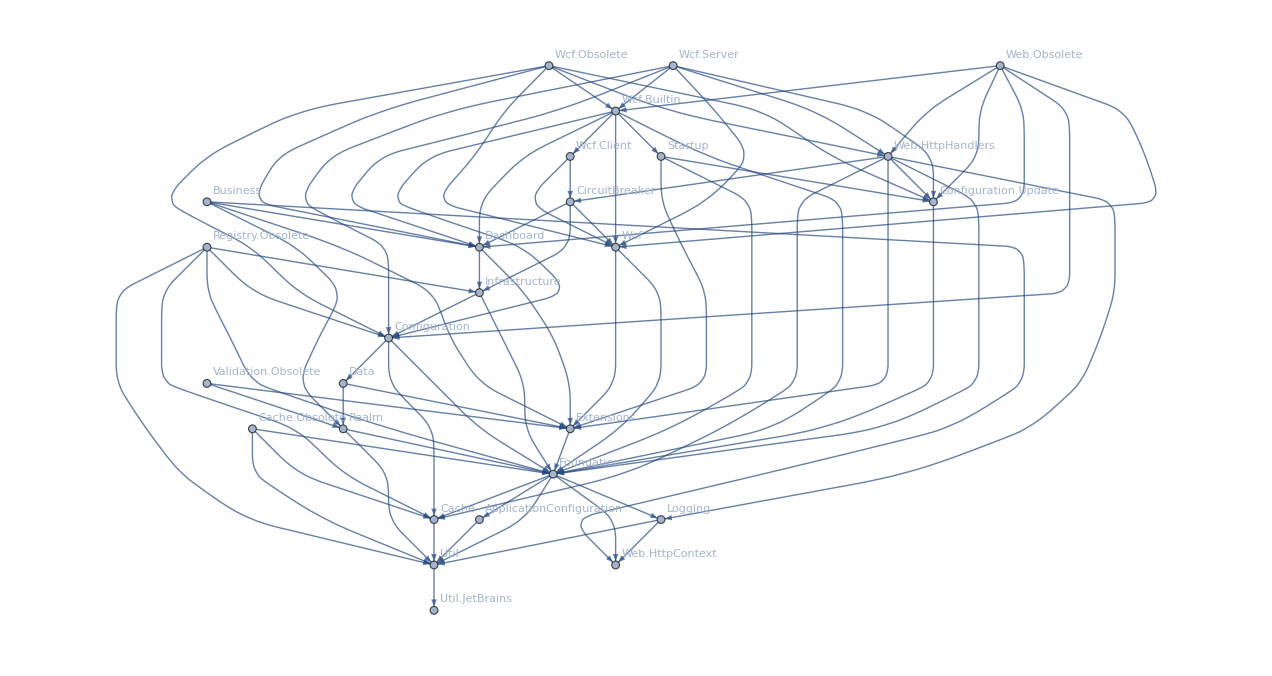

```mathematica
g=Graph[DeleteDuplicates[deps],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
```

```mathematica
SimplerGraph[g_]:=Block[{result=g, toDelete={},paths},
Table[
paths=FindPath[EdgeDelete[g,e],e[[1]],e[[2]]];
If[Length[paths]>0, AppendTo[toDelete,e]]
,{e,EdgeList[g]}
];
toDelete
]
```

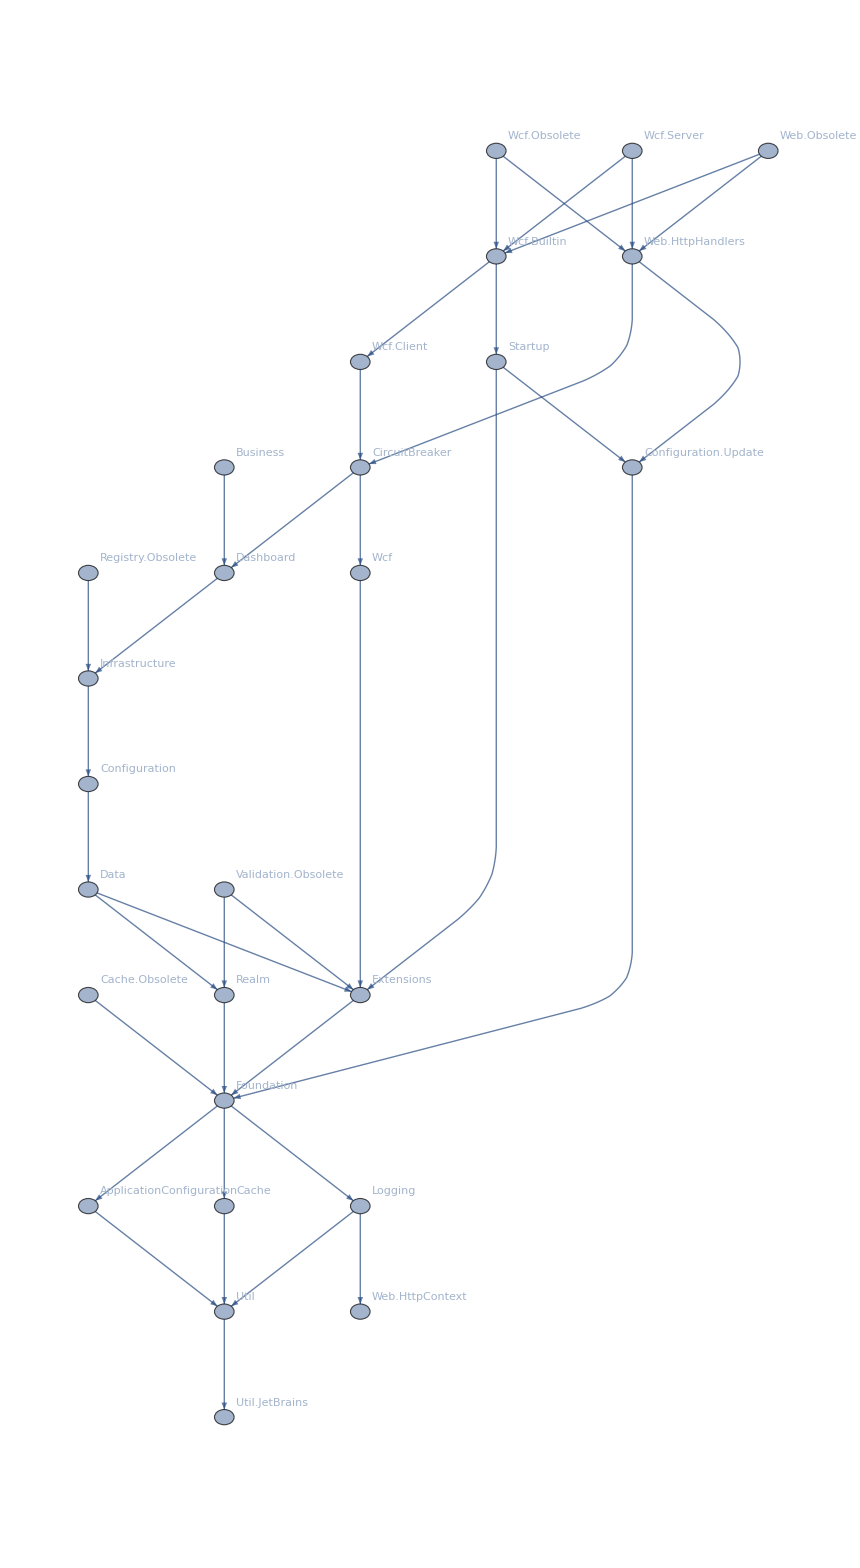

```mathematica
g2=EdgeDelete[g,SimplerGraph[g]]
```

```mathematica
VertexList[g]
```

{ApplicationConfiguration,Util,Business,Dashboard,Extensions,Realm,Web.HttpContext,Cache,Cache.Obsolete,Foundation,CircuitBreaker,Infrastructure,Wcf,Configuration,Data,Configuration.Update,Logging,Registry.Obsolete,Startup,Util.JetBrains,Validation.Obsolete,Wcf.Builtin,Wcf.Client,Wcf.Obsolete,Web.HttpHandlers,Wcf.Server,Web.Obsolete}

```mathematica
VertexCount[g]
```

27

```mathematica
m=MatrixPower[AdjacencyMatrix[g],2];m//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 3 | 0 | 1 | 2 | 0 | 3 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 3 | 0 | 1 | 0 | 0 | 2 | 1 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
With[{ver=VertexList[g]},Select[Flatten[Table[
If[m[[i,j]]>1,ver [[i]]<->ver[[j]],Null],{i,Length[m]},{j,Length[m]}],1],#=!=Null&]]
```

{Business<->Foundation,Dashboard<->Foundation,Cache.Obsolete<->Util,Foundation<->Util,CircuitBreaker<->Extensions,CircuitBreaker<->Foundation,Infrastructure<->Cache,Configuration<->Util,Data<->Foundation,Registry.Obsolete<->Util,Registry.Obsolete<->Cache,Registry.Obsolete<->Foundation,Startup<->Foundation,Validation.Obsolete<->Foundation,Wcf.Builtin<->Extensions,Wcf.Builtin<->Cache,Wcf.Builtin<->Foundation,Wcf.Obsolete<->Extensions,Wcf.Obsolete<->Cache,Wcf.Obsolete<->Foundation,Web.HttpHandlers<->Util,Web.HttpHandlers<->Web.HttpContext,Web.HttpHandlers<->Foundation,Wcf.Server<->Extensions,Wcf.Server<->Cache,Wcf.Server<->Foundation,Web.Obsolete<->Extensions,Web.Obsolete<->Cache,Web.Obsolete<->Foundation}

```mathematica
g2=g;Table[If[EdgeQ[g2,e],g2=EdgeDelete[g2,e];],{e,With[{ver=VertexList[g]},Select[Flatten[Table[
If[m[[i,j]]>1,ver [[i]]->ver[[j]],Null],{i,Length[m]},{j,Length[m]}],1],#=!=Null&]]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Select[VertexList[g2],StringContainsQ[#,"Obsolete"]&]
```

{Cache.Obsolete,Registry.Obsolete,Validation.Obsolete,Wcf.Obsolete,Web.Obsolete}

```mathematica
ReverseGraph
```

ReverseGraph

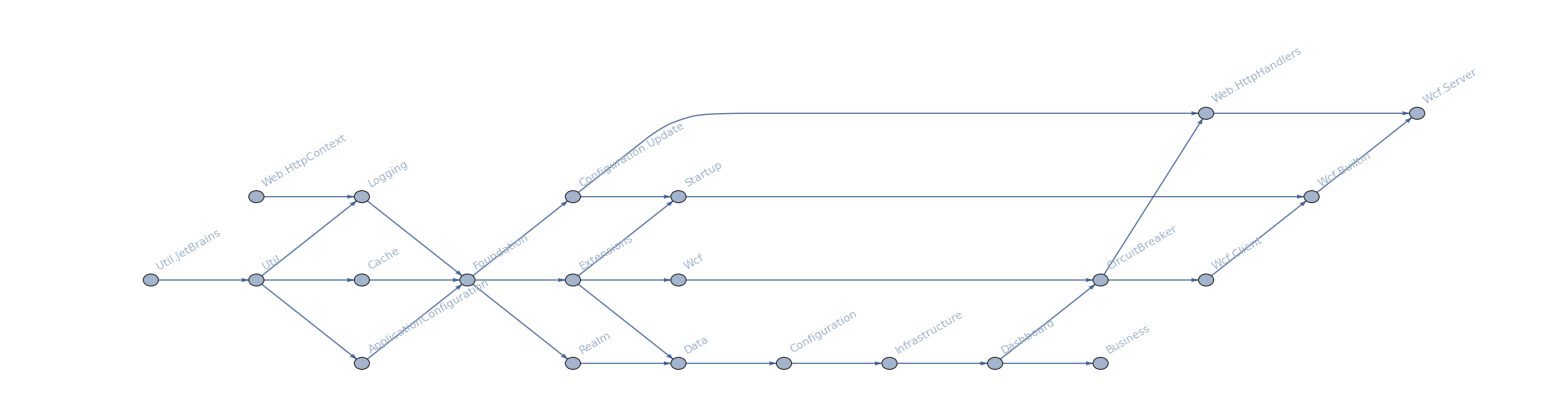

```mathematica
Graph[ReverseGraph[Graph[EdgeList[VertexDelete[g2,Select[VertexList[g2],StringContainsQ[#,"Obsolete"]&]]]]], VertexLabels->Map[#->Rotate[#,Pi/6]&,VertexList[VertexDelete[g,Select[VertexList[g2],StringContainsQ[#,"Obsolete"]&]]]], GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}, ImageSize->1600]
```

```mathematica
MatrixPower[AdjacencyMatrix[g2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 1 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 2 | 0 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
With[{m=MatrixPower[AdjacencyMatrix[g2],2]},
With[{ver=VertexList[g2]},Select[Flatten[Table[
If[m[[i,j]]>1,ver [[i]]<->ver[[j]],Null],{i,Length[m]},{j,Length[m]}],1],#=!=Null&]]
]
```

{Business<->Foundation,Dashboard<->Foundation,Foundation<->Util,CircuitBreaker<->Extensions,CircuitBreaker<->Foundation,Infrastructure<->Cache,Data<->Foundation,Registry.Obsolete<->Foundation,Startup<->Foundation,Validation.Obsolete<->Foundation,Wcf.Builtin<->Extensions,Wcf.Builtin<->Foundation,Wcf.Obsolete<->Extensions,Wcf.Obsolete<->Cache,Wcf.Obsolete<->Foundation,Web.HttpHandlers<->Util,Web.HttpHandlers<->Foundation,Wcf.Server<->Extensions,Wcf.Server<->Cache,Wcf.Server<->Foundation,Web.Obsolete<->Extensions,Web.Obsolete<->Cache,Web.Obsolete<->Foundation}

```mathematica
EdgeCount[g]
```

77

```mathematica
EdgeCount[g2]
```

69